R. Pure, S. Durrani, F. Tong and J. Pan, “Distance Distribution Between Two Random Nodes in Arbitrary Polygons,” Mathematical Methods in Applied Sciences, March 2020 (revised Jan. 2021)
Copyright: R. Pure and S. Durrani, 2021.
Tested in Mathematica 12.2

```mathematica
(*RandomPointsTriangle generates uniformly random points in a triangle*)
RandomPointsTriangle[{a_,b_,c_},n_]:=Module[{u,v},{u,v}=Transpose[Sort/@RandomReal[1,{n,2}]];
Map[# a&,u]+Map[# b&,(v-u)]+Map[# c&,(1-v)]]
```

```mathematica
(*RandomPointsPolygon generates uniformly random points in a polygon*)
RandomPointsPolygon[P_,n_]:=Module[{p,s,t},p=N[P];
(*Numerically approximate vertices for faster computation.*)
s=First/@MeshPrimitives[TriangulateMesh[DiscretizeGraphics@Graphics[p],MaxCellMeasure->Infinity],2];
t=Accumulate[Area[Polygon@#]/Area[p]&/@s];
(*Triangulate the polygon.Calculate the area of the polygon.
Associate each triangle with its fraction of area of the polygon.
Associate each triangle with a range calculated as the sum of all previous area fractions.
This allows a triangle to be picked from a random variable generated between 0 and 1.*)Select[Map[Function[x,Flatten@RandomPointsTriangle[s[[First@FirstPosition[x<#&/@t,True]]],1]],RandomReal[1,n]],#≠{}&]
(*Random points:Generate n random numbers between 0 and 1. For each random number,pick the corresponding triangle and generate a point in it.*)
]
```

```mathematica
(* Enable for Fig3: arbitrary polygons without holes*)
(*PolyBoundary1={{0,0},{3,0},{2,3},{2,1}};
  (*PolyBoundary2={{3,4},{7,4},{5,7},{3,6},{1,6}};*)
(*PolyBoundary2={{3,1},{7,1},{5,4},{3,3},{1,3}}; *)
PolyBoundary2={{0,0},{4,0},{2,3},{0,2},{-2,2}};
PolyHoles1={};
PolyHoles2={};*)

(* Enable for Fig5: arbitrary polygons with holes*)
PolyBoundary1={{0,0},{3,0},{2,3},{2,1}};
PolyHoles1={{{2,0.2},{2,0.4},{2.4,0.4},{2.4,0.2}},{{1,0.2},{1,0.4},{1.8,0.4}}};
PolyBoundary2={{3,4},{7,4},{5,7},{3,6},{1,6}}; 
PolyHoles2={{{3,4.5},{6,4.5},{5,6}}};

Poly1=If[Length@PolyHoles1≠0,Polygon[PolyBoundary1->PolyHoles1],Polygon@PolyBoundary1];
Poly2=If[Length@PolyHoles2≠0,Polygon[PolyBoundary2->PolyHoles2],Polygon@PolyBoundary2];
pic1=Graphics[{Opacity[0.5],Blue,Poly1}];
pic2=Graphics[{Opacity[0.5], Red,Poly2}];
Show[pic1, pic2, PlotRange->Automatic, Frame->True]
```

-Graphics-

```mathematica
n=4000;
data1=RandomPointsPolygon[Poly1,n];
data2=RandomPointsPolygon[Poly2,n];
data=Norm[#[[1]]-#[[2]]]&/@Tuples[{data1,data2}];
dist=SmoothKernelDistribution@data;
min=Min@data;
max=Max@data;
Clear[data1,data2,data];
ClearSystemCache[];
```

```mathematica
ShiftedPolygon[vertices_,r_,θ_]:=Polygon[#+{r Cos[θ],r Sin[θ]}&/@vertices]
ShiftedPolygonBoundaryIntersectionArea[poly1Boundary_,poly2_,r_,θ_]:=Area@RegionIntersection[ShiftedPolygon[poly1Boundary,r,θ],Polygon@poly2]
ShiftedPolygonWithHolesIntersectionArea[poly1Boundary_,poly1Holes_,poly2Boundary_,r_,θ_]:=ShiftedPolygonBoundaryIntersectionArea[poly1Boundary,poly2Boundary,r,θ]-Total[ShiftedPolygonBoundaryIntersectionArea[#,poly2Boundary,r,θ]&/@poly1Holes]
ShiftedIntersectionArea[r_,θ_]:=ShiftedPolygonWithHolesIntersectionArea[PolyBoundary1,PolyHoles1,PolyBoundary2,r,θ]-Total[ShiftedPolygonWithHolesIntersectionArea[PolyBoundary1,PolyHoles1,#,r,θ]&/@PolyHoles2]
```

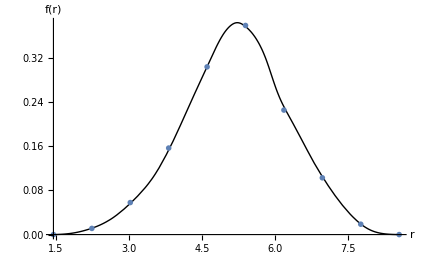

```mathematica
pts=9;
divs=200;
t=Table[{r,(2 π r)/(divs (Area@Poly1)(Area@Poly2)) Total@Table[ShiftedIntersectionArea[r,θ],{θ,0,2 π,(2 π)/divs}]},{r,min,max,(max-min)/pts}];
Show[Plot[PDF[dist,x],{x,min,max},PlotStyle->{Black,Thick},PlotLegends->Placed[{"Simulated PDF"},{0.85,0.82}]],ListPlot[t,PlotMarkers->Style["X",{Red,FontSize->15}],PlotLegends->Placed[{"Theoretical PDF"},{0.85,0.82}]],AxesLabel->{"r","f(r)"},LabelStyle->Directive[Bold,20],TicksStyle->Directive[Plain,15]]
```